## color_changed bar

6

a is 67.2056

6

a is 151.529

4

a is 474.283

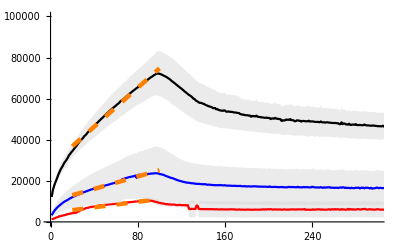

```mathematica
folder = "/Users/csfloyd/Dropbox/Projects/TCB2Network/prompt_long_pulse/";
(*resultFolder = "/media/xlei45/Extreme Pro/mathematica_code/result";*)
filePatterns = {"50um*3*1*.txt", "75um*3*1*.txt", "100um*3ul*1ul*.txt"};
plots = {};
colors = {Transparent, Red, Transparent, Transparent, Blue, 
   Transparent, Transparent, Black, Transparent}; (* List of colors *)
equations = {};

i = 1;
tMax = 300;
t1 = 20;
t2 = 100;
unit = 1/2.33^2;
Do[
  files = FileNames[pattern, folder];
Print[Length[files]];
  data = DeleteCases[#, 0] & /@ (ReadList[#, Number] & /@ files);
  data = DeleteCases[data, {}] * unit;
  minLength = Min[Length /@ data];
  truncatedData = Take[#, minLength] & /@ data;
  meanData = Mean /@ Transpose[truncatedData];
  stdData = StandardDeviation /@ Transpose[truncatedData];
  upper = meanData + stdData;
  lower = meanData - stdData;

  (* fit a fourth degree polynomial model *)
tRange = Range[Length[meanData]];
data = Transpose[{tRange, meanData}];
nlm=NonlinearModelFit[data[[t1;;t2]],a*x+b,{a,b},x];

Print["a is ",a/.nlm["BestFitParameters"]];

  (* create plots for both the data and the fit *)
  plotData = ListLinePlot[{lower, meanData, upper}, 
        Filling -> {1 -> {3}}, 
        PlotStyle -> {colors[[i]], colors[[i + 1]], colors[[i + 2]]}, 
        FillingStyle -> Directive[Opacity[0.5], LightGray], 
        FrameLabel -> {"Time (s)", " Area (pixel^2)"}, 
        PlotRange -> {{0, tMax}, {0, 100000}}];

plotFit= Plot[nlm[x],{x,t1,t2},PlotStyle->{Dashing[0.02],Orange,Thickness[0.008]}];
  (* append both plots to the list of plots *)
  AppendTo[plots, plotData];
  AppendTo[plots, plotFit];

  i = i + 3;,
 {pattern, filePatterns}] 

Show[plots]

(*Export[FileNameJoin[{resultFolder, "50um75um100umLongTerm.png"}], plots]

Print[equations]*)
```

```mathematica
meanData[[1]]
```

28226.8

```mathematica
Pi*100^2//N
```

31415.9

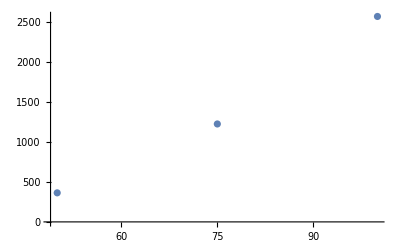

```mathematica
ListPlot[{{50,364},{75,1227},{100,2574}}]
```

6

a is 67.2056

3

a is 226.099

4

a is 474.283

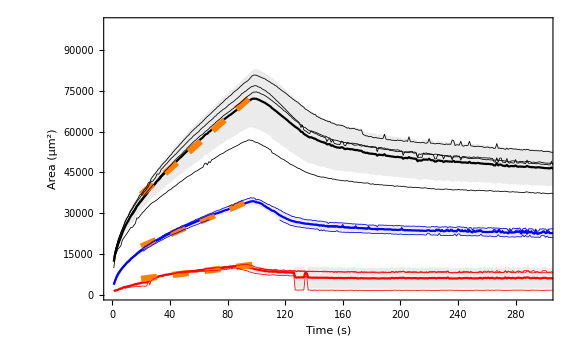

```mathematica
SetOptions[ListLinePlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

older = "/Users/csfloyd/Dropbox/Projects/TCB2Network/prompt_long_pulse/";
(*resultFolder = "/media/xlei45/Extreme Pro/mathematica_code/result";*)
filePatterns = {"50um*3*1*.txt", "75um*3*1*.txt", "100um*3ul*1ul*.txt"};
filePatterns = {"50um*3*1*.txt", "75um*1*1*1*.txt", "100um*3ul*1ul*.txt"};
filePatterns = {"50um*3*1*.txt", "75um*3ul*1ul*.txt", "100um*3ul*1ul*.txt"};


plots = {};
colors = {Transparent, Red, Transparent, Transparent, Blue, 
   Transparent, Transparent, Black, Transparent}; (* List of colors *)
equations = {};

i = 1;
tMax = 300;
t1 = 20;
t2 = 100;
unit = 1/2.33^2;

as = {};

Do[
  files = FileNames[pattern, folder];
Print[Length[files]];
  data = DeleteCases[#, 0] & /@ (ReadList[#, Number] & /@ files);
  data = DeleteCases[data, {}] * unit;
  minLength = Min[Length /@ data];
  truncatedData = Take[#, minLength] & /@ data;
  meanData = Mean /@ Transpose[truncatedData];
  stdData = StandardDeviation /@ Transpose[truncatedData];
  upper = meanData + stdData;
  lower = meanData - stdData;

  (* fit a fourth degree polynomial model *)
tRange = Range[Length[meanData]];
data = Transpose[{tRange, meanData}];
nlm=NonlinearModelFit[data[[t1;;t2]],a*x+b,{a,b},x];

Print["a is ",a/.nlm["BestFitParameters"]];

  (* create plots for both the data and the fit *)
  plotData = ListLinePlot[{lower, meanData, upper}, 
        Filling -> {1 -> {3}}, 
ImageSize->Large,
        PlotStyle -> {colors[[i]], colors[[i + 1]], colors[[i + 2]]}, 
        FillingStyle -> Directive[Opacity[0.5], LightGray], 
        FrameLabel -> {"Time (s)", " Area (μm^2)"}, 
        PlotRange -> {{0, tMax}, {0, 100000}}];


plotFit= Plot[nlm[x],{x,t1,t2},PlotStyle->{Dashing[0.02],Orange,Thickness[0.008]}];

  (* append both plots to the list of plots *)
  AppendTo[plots, plotData];
  AppendTo[plots, plotFit];

subas = {};
Do[
AppendTo[plots, ListLinePlot[Transpose[{tRange,truncatedData[[f]]}], PlotStyle -> {Directive[colors[[i+1]],Thickness[0.001]]} ]];

tRange = Range[Length[meanData]];
data = Transpose[{tRange, truncatedData[[f]]}];
nlm=NonlinearModelFit[data[[t1;;t2]],a*x+b,{a,b},x];
AppendTo[subas, a/.nlm["BestFitParameters"]];

,{f,1,Length[truncatedData]}];
AppendTo[as,subas];
  i = i + 3;,
 {pattern, filePatterns}] 

Show[plots]
```

```mathematica
th = 0.004;

legend=LineLegend[
{Directive[Red], Directive[Blue], Directive[Black]},{"50","75","100"},LegendLayout->"Row", LegendLabel->"r_0",LabelStyle->{FontSize->16}];
```

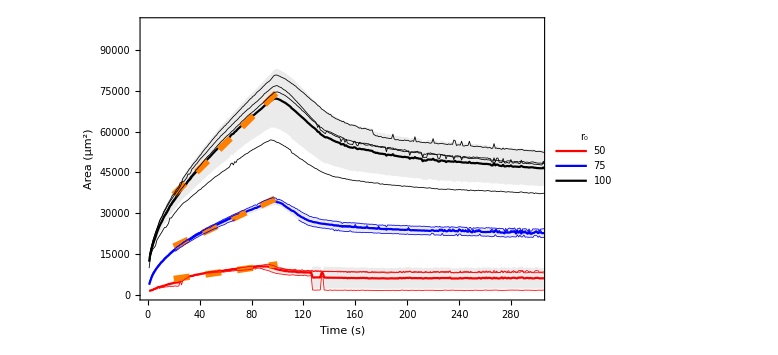

```mathematica
Legended[Show[plots],Placed[legend,{{0.7,0.9},{0.5,0.9}}]]
```

```mathematica
lpData = {};
r0s = {50,75,100};
Do[
subas = as[[i]];
Do[
AppendTo[lpData, {r0s[[i]],subas[[j]]}]
,{j,1,Length[subas]}]
,{i,1,3}]
```

```mathematica
lpData
```

{{50,72.5545},{50,54.9529},{50,74.1093},{75,225.803},{75,214.147},{75,238.347},{100,508.166},{100,350.514},{100,495.378},{100,543.073}}

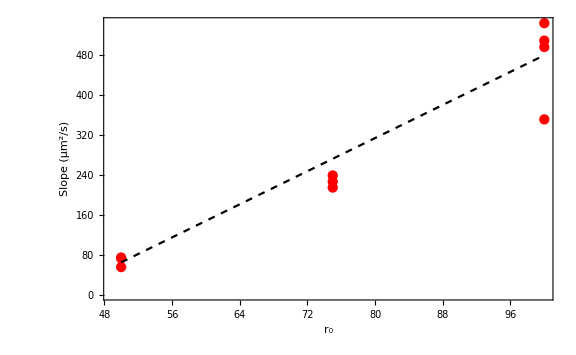

```mathematica
Show[
ListPlot[lpData, PlotStyle->Red, FrameLabel->{"r_0","Slope (μm^2/s)"}, PlotRange->Full,ImageSize->Large],
Plot[45*x*unit-350,{x,50,100}, PlotStyle->Directive[Black,Dashed]]
]
```